```mathematica
data = Import["/Users/yangm/Desktop/p1b.xlsx"];
data = data[[1]];
```

```mathematica
k = data[[All,1]];
S = data[[All,2]];
d = data[[All,3]];
result = data[[All,4]];
```

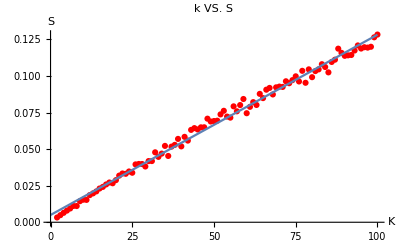

```mathematica
set1= Transpose@{k, S};
linear=Fit[set1,{1,x},x];
Show[ListPlot[set1,PlotStyle->Red],Plot[linear,{x,0,100}],PlotLabel->"k VS. S",AxesLabel->{"K", "S"},LabelStyle->Directive[Blue]]
```

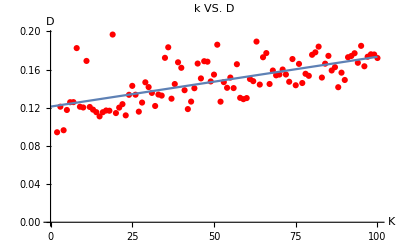

```mathematica
set2= Transpose@{k, d};
linear=Fit[set2,{1,x},x];
Show[ListPlot[set2,PlotStyle->Red],Plot[linear,{x,0,100}],PlotLabel->"k VS. D",AxesLabel->{"K", "D"},LabelStyle->Directive[Blue]]
```

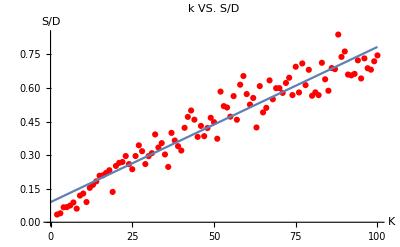

```mathematica
set3= Transpose@{k, result};
linear=Fit[set3,{1,x},x];
Show[ListPlot[set3,PlotStyle->Red],Plot[linear,{x,0,100}],PlotLabel->"k VS. S/D",AxesLabel->{"K", "S/D"},LabelStyle->Directive[Blue]]
```